# Scaffold protein titration motif

## The model description

This particular motif describe one phosphorylation-desphosphorylation cycle (can be generalized to any futile cycles) with both kinase (K) and phosphatase (P) can be titrated by a scaffold protein (T).

K + S ⇌ KS → K + S_p
P + S_p ⇌ PS_p → P + S
T + K ⇌ TK
T + P ⇌ TP
∅ → T
T → ∅ 

The above reactions show a simple system that composed of one scaffold protein, one kinase, one phosphatase and one substrate. Here we try to descibe this simple system with differential equation following the mass action kinetics.

ⅆ[K]/ⅆt=-k[1][K][S]+k[2][KS]+k[3][KS]-k[7][T][K]+k[8][TK],
ⅆ[P]/ⅆt=-k[4][P][S_p]+k[5][PS_p]+k[6][PS_p]-k[9][T][P]+k[10][TP],
ⅆ[S]/ⅆt=-k[1][K][S]+k[2][KS]+k[6][PS_p],
ⅆ[S_p]/ⅆt=-k[4][P][S_p]+k[3][KS]+k[5][PS_p],
ⅆ[KS]/ⅆt=k[1][K][S]-k[2][KS]-k[3][KS],
ⅆ[PS_p]/ⅆt=k[4][P][S_p]-k[5][PS_p]-k[6][PS_p],
ⅆ[T]/ⅆt=-k[7][T][K]+k[8][TK]-k[9][T][P]+k[10][TP] + k[11]k_d-k_d[T],
ⅆ[TK]/ⅆt=k[7][T][K]-k[8][TK],
ⅆ[TP]/ⅆt=k[9][T][P]-k[10][TP].

And the system need to follow these conservation equations:

[K]+[KS]+[TK]=[K_tot],
[P]+[PS_p]+[TP]=[P_tot],
[S]+[S_p]+[KS]+[PS_p]=[S_tot],
[T]+[TK]+[TP]=[T_tot].

In the following setion, we will solve the differential equations to understand the dynamics and behaviour of such system.

## Understanding the dynamics of the simple system with input pertubations (numerical study)

Since, it is a bit difficult to solve the differential equations analytically. Here we try to study them numerically. By defining two different way to characterising the dynamics with scoring their tempral dynamics when presented with input signal perturbation (the changing of [T]). The quantification can be derived from the actually fitness funcitons for ultrasensitive response and adaptive response. Then we save all the parameter sets as well as their score on ultrasensitivity and adaptation.

```mathematica
Clear["Global`*"];
SetDirectory[NotebookDirectory[]];
kd=10;
des={-k[1]* x[1][t] *x[3][t]+k[2]* x[5][t]+k[3] *x[5][t]-k[7]* x[1][t]* x[7][t]+k[8]*x[8][t],-k[4]* x[2][t] *x[4][t]+k[5]* x[6][t]+k[6] *x[6][t]-k[9]* x[2][t]* x[7][t]+k[10]* x[9][t],-k[1]* x[1][t] *x[3][t]+k[2] *x[5][t]+k[6]*x[6][t],
-k[4]*x[2][t]* x[4][t]+k[3]*x[5][t]+k[5]* x[6][t],
k[1]* x[1][t] *x[3][t]-k[2] *x[5][t]-k[3]* x[5][t],
k[4] *x[2][t]* x[4][t]-k[5] *x[6][t]-k[6] *x[6][t],-k[7] *x[1][t]* x[7][t]-k[9] *x[2][t]* x[7][t]+k[8]* x[8][t]+k[10]*x[9][t]+k11[t]*kd-kd*x[7][t],
k[7]* x[1][t] *x[7][t]-k[8]* x[8][t],
k[9] *x[2][t] *x[7][t]-k[10] *x[9][t],0};

init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};(*init={tot[1],tot[2],tot[3],0.00001,0.00001,0.00001,totT,0.00001,0.00001};*)
```

```mathematica
AbsoluteTiming[
totK=0.1;totP=0.1;totS=0.1;
stepNum=5;
sampleSize=100000;

pars={};
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];
SeedRandom[IntegerPart[SessionTime[]]];
ts={};
For[num=1,num≤sampleSize,num++,
Block[{k,T,ssthreshold},k[n_]:=k[n]=10^(RandomReal[]*6-3);
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
totT=1.*^-4;
(*totT=1.*10^(RandomReal[]*4-3);*)

Block[{tPer,step},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]},vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

ks=Array[k,10];
AppendTo[pars,Join[ks,{totT,totK,totP,totS,us,ad,num,(ks[[2]]+ks[[3]])/ks[[1]],(ks[[5]]+ks[[6]])/ks[[4]],ks[[8]]/ks[[7]],ks[[10]]/ks[[9]]}]];
];
];
];
];
]

(*Plot@@{{{(x[7][t]+x[8][t]+x[9][t]),x[4][t]}/.sol},Flatten@{t,x[1]["Domain"]/.sol},PlotLegends->{"T_tot","S_p"}}
ListPlot[Transpose@{xT,x4},PlotRange->{0,10}]*)
(*Print[pars];*)
transPars=Transpose[pars];
(*Export["saturationSampling.csv",transPars];*)
Export["unsaturationSampling.csv",transPars];
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 493.446 and t = 509.237.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 660.999 and t = 663.826.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 541.169 and t = 541.223.

General::stop: Further output of NDSolve :: evcvmit will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-0.000378035} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

{22627.9,Null}

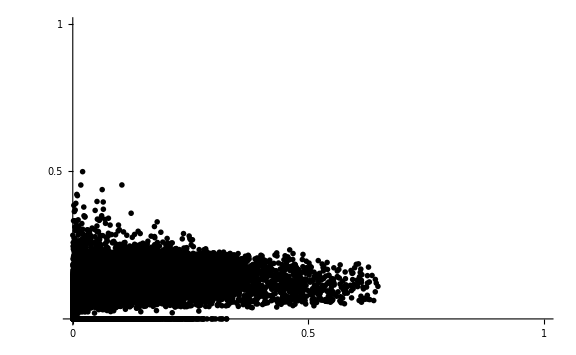

```mathematica
ListPlot[Transpose[{transPars[[15]],transPars[[16]]}],PlotRange->{{0,1},{0,1}},(*AxesLabel->{"Ultrasensitive score","Adaptive score"},*)Ticks->{{0,0.5,1}, {0.5,1}},PlotStyle->{Thick,PointSize[0.01]},PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

```mathematica
maxAndIndex[a_]:={#,First@SparseArray[UnitStep[a-#]]["AdjacencyLists"]}&@Max@a
```

```mathematica
maxAndIndex[transPars[[15]]]
```

{0.648184,77503}

```mathematica
maxAndIndex[transPars[[16]]]
```

{0.498665,8916}

```mathematica
usIndex=maxAndIndex[transPars[[15]]]//Last;
adIndex=maxAndIndex[transPars[[16]]]//Last;
pars[[usIndex]]
```

{8.65972,0.172201,120.995,0.00560095,4.41017,227.682,146.183,0.00204916,1.82932,1.75143,0.0001,0.1,0.1,0.1,0.648184,0.110249,77503,13.992,41438.1,0.0000140178,0.957421}

```mathematica
pars[[adIndex]]
```

{546.653,2.55024,233.149,174.475,0.00278461,135.035,0.226778,0.00977263,229.077,16.2045,0.0001,0.1,0.1,0.1,0.0208979,0.498665,8916,0.431169,0.773964,0.0430935,0.0707383}

{a→0.982701,b→0.292601,hillK→1560.85,n→1.7146}

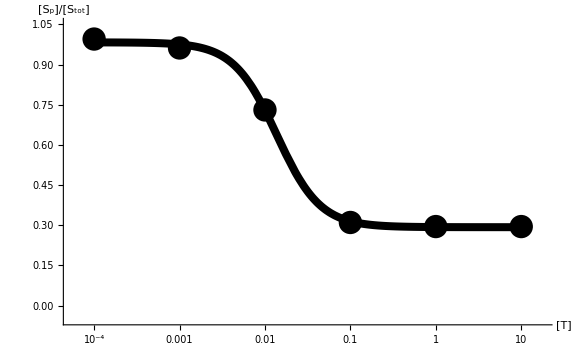

```mathematica
init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};
maxAndIndex[a_]:={#,First@SparseArray[UnitStep[a-#]]["AdjacencyLists"]}&@Max@a
usIndex=maxAndIndex[transPars[[15]]]//Last;
adIndex=maxAndIndex[transPars[[16]]]//Last;
stepNum=5;
maxPars=Solve[Array[k,10]==pars[[usIndex]][[Range[10]]]];totT=0.0001;
Block[{tPer,step},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[(Norm[df]<ssthreshold),{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol]/totS;k11t=Evaluate[(k11[ts-0.001])/.sol];
];
fittedHill=FindFit[Transpose@{k11t,x4},a+(b-a)*hillK/(hillK+x^(-n)),{a,b,hillK,n},x]
Show[LogLinearPlot[a+(b-a)*hillK/(hillK+x^(-n))/.fittedHill,{x,10^-4,10},(*Ticks->{Automatic,{0,0.5,1}},*) PlotRange->{-0.05,1.05}, AxesLabel->{"[T]","[S_p]/[S_tot]"},PlotTheme->"Monochrome",PlotStyle->{Thickness[0.01]}],ListLogLinearPlot[Transpose@{k11t,x4},PlotTheme->"Monochrome",PlotMarkers->{Automatic,24}], PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

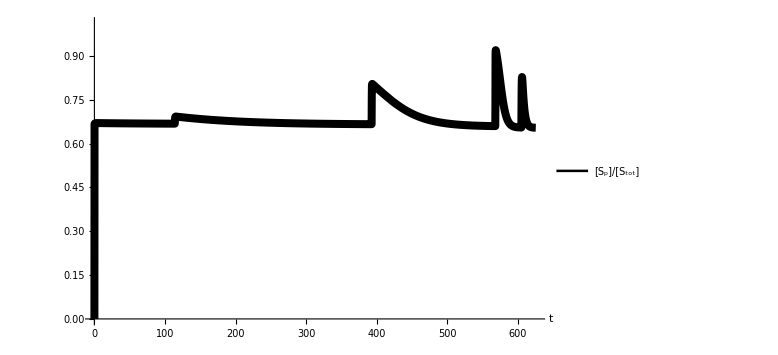

```mathematica
init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};
maxPars=Solve[Array[k,10]==pars[[adIndex]][[Range[10]]]];totT=0.0001;
Block[{tPer,step},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol];k11t=Evaluate[(k11[ts-0.001])/.sol];
];
Plot[{{x[4][t]/totS}/.sol},{t,0,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[S_p]/[S_tot]"},{0.85,0.85}],PlotRange->{0,1.01},AxesLabel->{"t"},PlotTheme->"Monochrome",PlotStyle->{Thickness[0.01]}, PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t = 274.926 and t = 287.122.

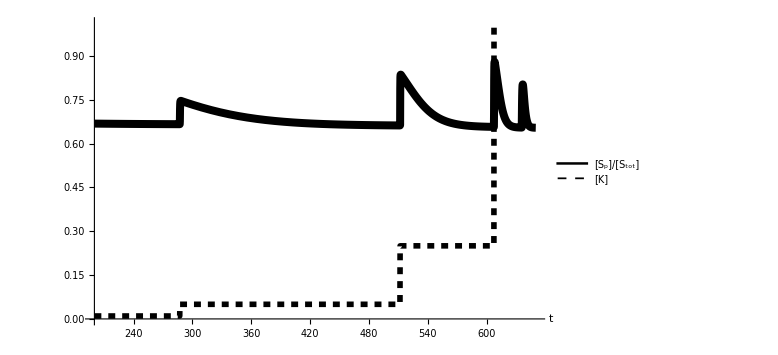

```mathematica
init={totK,totP,totS,0,0,0,totT,0,0,0.01};
stepNum=4;
maxPars=Solve[Array[k,10]==pars[[adIndex]][[Range[10]]]];totT=0.0001;
Block[{tPer,step},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->5*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
x4=Evaluate[x[4][ts-0.001]/.sol];k11t=Evaluate[(k11[ts-0.001])/.sol];
];
Show[Plot[{{x[4][t]/totS}/.sol},{t,200,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[S_p]/[S_tot]"},{0.25,0.95}],PlotRange->{0,1.01},AxesLabel->{"t"},PlotTheme->"Monochrome",PlotStyle->{Thickness[0.01]}, PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large],Plot[{{k11[t]}/.sol},{t,200,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[K]"},{0.55,0.95}],PlotRange->{0,1.01},AxesLabel->{"t"},PlotTheme->"Monochrome",PlotStyle->{Dashed,Thickness[0.007]}, PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]]
```

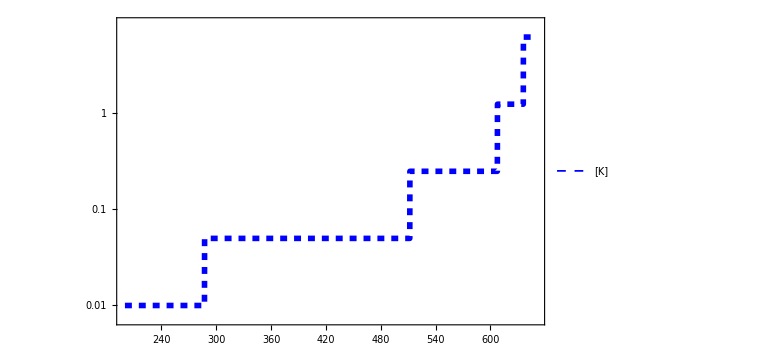

```mathematica
input=LogPlot[{{k11[t]}/.sol},{t,200,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[K]"},{0.15,0.9}],PlotTheme->"Monochrome", PlotStyle->{Blue,Dashed,Thickness[0.007]},Ticks->{},LabelStyle->{18,GrayLevel[0]},ImageSize->Large,ImagePadding->50,Frame->{True,True,False,False},FrameStyle->{Automatic,Blue,Automatic,Automatic}]
```

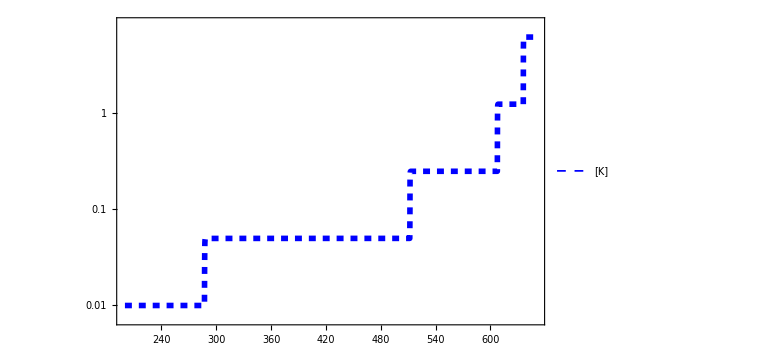

```mathematica
actualInput=LogPlot[{{x[7][t]}/.sol},{t,200,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[K]"},{0.65,0.15}],PlotTheme->"Monochrome", PlotStyle->{Blue,Dashed,Thickness[0.007]},Ticks->{},LabelStyle->{18,GrayLevel[0]},ImageSize->Large,ImagePadding->50,Frame->{True,True,False,False},FrameStyle->{Automatic,Blue,Automatic,Automatic}]
```

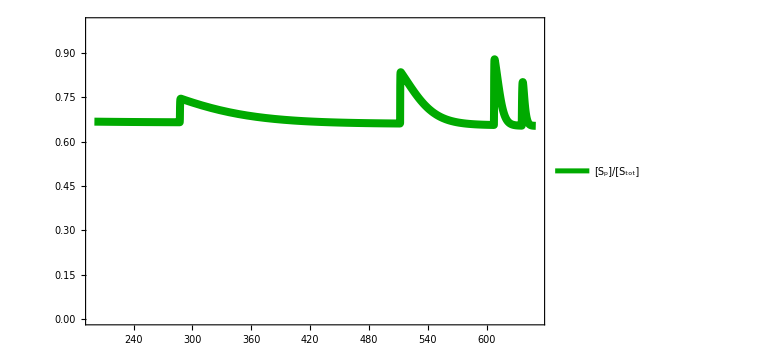

```mathematica
output=Plot[{{x[4][t]/totS}/.sol},{t,200,ts[[stepNum+1]]-0.01},PlotLegends->Placed[{"[S_p]/[S_tot]"},{0.4,0.9}],PlotRange->{0,1},PlotStyle->{Darker[Green],Thickness[0.01]},Ticks->{0,0.5,1},LabelStyle->{18,GrayLevel[0]},ImageSize->Large,ImagePadding->50,(*Axes->False,*)Frame->{False,False,False,True},FrameTicks->{None,None,None,{0,0.5,1}},FrameStyle->{Automatic,Automatic,Automatic,Darker[Green]}]
```

```mathematica
adPlot=Overlay[{output,input}]
Export["scaffoldTitrationUnsaturatedVaringTAd.eps",adPlot];
Export["scaffoldTitrationUnsaturatedVaringTAd.pdf",adPlot];
```

-Graphics--Graphics-

```mathematica
us1000index=Reverse[Ordering[transPars[[15]],-1000]];
```

```mathematica
ad1000index=Reverse[Ordering[transPars[[16]],-1000]];
```

```mathematica
us1000pars=pars[[us1000index]];
```

```mathematica
ad1000pars=pars[[ad1000index]];
```

```mathematica
ListPointPlot3D[Transpose[{Log10[Transpose[us1000pars][[18]]],Log10[Transpose[us1000pars][[19]]],Transpose[us1000pars][[15]]}],ColorFunction->"Rainbow",ImageSize->Large,PlotRange->Full]
```

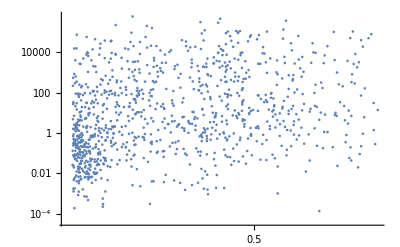

```mathematica
ListLogLogPlot[Transpose[{Transpose[us1000pars][[15]],Transpose[us1000pars][[18]]}]]
```

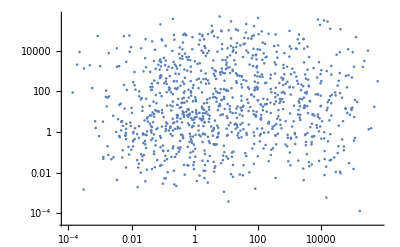

```mathematica
ListLogLogPlot[Transpose[{Transpose[us1000pars][[18]],Transpose[us1000pars][[19]]}]]
```

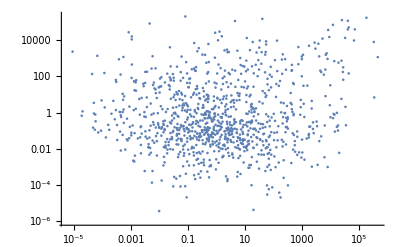

```mathematica
ListLogLogPlot[Transpose[{Transpose[ad1000pars][[18]],Transpose[ad1000pars][[19]]}]]
```

## Past

```mathematica
us10index=Reverse[Ordering[transPars[[15]],-10]]
```

{77503,85694,95713,42299,48178,25993,79997,14745,86233,53343}

```mathematica
ad10index=Reverse[Ordering[transPars[[16]],-10]]
```

{8916,43846,63403,92229,75615,91669,74646,27646,27024,37636}

```mathematica
us10pars=pars[[us10index]]
```

{{8.65972,0.172201,120.995,0.00560095,4.41017,227.682,146.183,0.00204916,1.82932,1.75143,0.0001,0.1,0.1,0.1,0.648184,0.110249,77503,13.992,41438.1,0.0000140178,0.957421},{272.541,77.3858,0.00492018,6.19299,35.3706,1.15547,0.881511,0.197247,3.387,0.00664123,0.0001,0.1,0.1,0.1,0.644631,0.12127,85694,0.28396,5.89797,0.22376,0.0019608},{19.5244,27.4583,0.0130764,2.56091,0.00812433,0.0100659,0.206922,0.0698222,224.765,0.0272651,0.0001,0.1,0.1,0.1,0.642727,0.133686,95713,1.40702,0.00710304,0.337433,0.000121305},{2.43644,1.00522,74.5767,0.118069,51.6352,14.1163,547.384,0.140525,0.765167,0.129172,0.0001,0.1,0.1,0.1,0.642563,0.0917216,42299,31.0215,556.891,0.00025672,0.168816},{0.00982216,124.499,663.871,12.5465,2.17056,87.5917,6.14634,2.23875,112.171,0.00145326,0.0001,0.1,0.1,0.1,0.639291,0.0622569,48178,80264.4,7.15439,0.364241,0.0000129557},{0.0128001,2.96206,654.524,54.1296,10.4273,0.0523344,0.0709678,0.0258701,2.80597,0.00223411,0.0001,0.1,0.1,0.1,0.635739,0.147139,25993,51365.6,0.193602,0.364532,0.000796199},{2.44821,300.262,105.785,0.00976895,0.00143653,219.138,68.7424,0.019436,4.18432,1.16783,0.0001,0.1,0.1,0.1,0.630743,0.0654535,79997,165.854,22432.2,0.000282737,0.279097},{61.5883,376.142,0.0828141,1.94802,0.702829,162.173,0.0654196,0.0188604,19.8386,0.00193411,0.0001,0.1,0.1,0.1,0.629929,0.125224,14745,6.10871,83.6109,0.288299,0.000097492},{0.00502998,0.00495518,96.7688,0.875998,0.00541958,0.679301,11.1544,13.6049,73.5868,0.00697215,0.0001,0.1,0.1,0.1,0.628227,0.0663977,86233,19239.4,0.781647,1.21969,0.0000947472},{0.0547582,0.0344655,0.0167663,43.1099,1.41007,0.0109827,6.6196,2.33783,7.93527,0.00467318,0.0001,0.1,0.1,0.1,0.628177,0.17545,53343,0.9356,0.0329634,0.353168,0.000588913}}

```mathematica
ad10pars=pars[[ad10index]]
```

{{546.653,2.55024,233.149,174.475,0.00278461,135.035,0.226778,0.00977263,229.077,16.2045,0.0001,0.1,0.1,0.1,0.0208979,0.498665,8916,0.431169,0.773964,0.0430935,0.0707383},{170.189,9.37083,101.362,138.484,0.00447956,65.6978,0.172123,0.00289269,1.90607,0.0283304,0.0001,0.1,0.1,0.1,0.104317,0.453719,43846,0.650647,0.474439,0.0168059,0.0148633},{75.054,0.0220672,38.1592,956.071,0.0351052,59.3196,0.873047,0.00251072,51.455,0.125673,0.0001,0.1,0.1,0.1,0.0171,0.453446,63403,0.508717,0.0620819,0.00287582,0.00244239},{25.0255,0.340223,137.143,21.0531,0.0373125,251.016,0.259899,0.00570669,16.3015,0.298008,0.0001,0.1,0.1,0.1,0.0624876,0.437868,92229,5.4937,11.9247,0.0219574,0.018281},{222.612,0.0383764,185.495,50.5673,0.18893,20.5795,247.462,0.23876,1.33938,0.00295779,0.0001,0.1,0.1,0.1,0.00858596,0.421726,75615,0.833439,0.410708,0.000964837,0.00220833},{70.8515,5.47391,79.0432,364.847,0.00928001,6.40364,890.968,2.59989,0.907488,0.00322297,0.0001,0.1,0.1,0.1,0.00978986,0.417404,91669,1.19288,0.017577,0.00291806,0.00355153},{155.97,0.0414782,31.8275,150.072,0.729647,0.132826,72.3127,0.0231427,844.747,5.07664,0.0001,0.1,0.1,0.1,0.0514743,0.397776,74646,0.204328,0.00574707,0.000320036,0.00600966},{14.359,7.017,201.964,39.3731,38.928,267.787,34.5758,0.575732,0.334687,0.00458499,0.0001,0.1,0.1,0.1,0.0646745,0.396018,27646,14.554,7.78995,0.0166513,0.0136993},{70.4956,0.253549,3.94263,39.6001,0.952506,0.0897251,960.418,0.074313,1.0355,0.00272277,0.0001,0.1,0.1,0.1,0.00651779,0.391473,27024,0.059524,0.0263189,0.0000773757,0.00262942},{211.761,1.80245,6.67589,704.162,1.90868,10.3507,0.687989,0.00504778,576.502,18.5839,0.0001,0.1,0.1,0.1,0.00221222,0.384634,37636,0.0400373,0.0174098,0.007337,0.0322356}}

```mathematica
us10pars={{8.659720616637692,0.17220081639523258,120.99458521281544,0.005600946991795603,4.4101686490616006,227.68219811587858,146.1825887598013,0.002049159372782687,1.82931815538427,1.7514282396540004,0.0001,0.1,0.1,0.1,0.6481835551369277,0.11024895997827576,77503,13.991997131687611,41438.058082841075,0.000014017807388469133,0.9574213400216828},{272.54086216478066,77.3857505557688,0.00492018155307298,6.19298631753839,35.370579640607076,1.1554746114672112,0.8815107819439019,0.1972471051615054,3.3869993864490695,0.006641233576775582,0.0001,0.1,0.1,0.1,0.6446306854657481,0.12126961706068892,85694,0.283959880814242,5.897971088460727,0.22376028654639635,0.0019608015293260065},{19.52442234323404,27.458257216077104,0.013076385997428016,2.560914172479744,0.00812433499985589,0.01006594721577015,0.2069217688853947,0.06982221560037337,224.76504250713856,0.027265050129168186,0.0001,0.1,0.1,0.1,0.6427265334266281,0.13368580294464866,95713,1.4070241423349665,0.007103042503768219,0.33743291475071896,0.00012130467364960565},{2.436438483510556,1.0052202830100956,74.57670780235985,0.11806899466744147,51.63519903454336,14.11633947138184,547.3840049075174,0.14052464592627698,0.7651665558833731,0.12917245947693648,0.0001,0.1,0.1,0.1,0.6425629919676937,0.09172160220834255,42299,31.02148016331908,556.8908136392962,0.0002567204095596823,0.16881613353815347},{0.009822158419985284,124.49851569198056,663.8711772454718,12.54645445774545,2.170555332679573,87.59166636134162,6.146335639156246,2.2387462851336486,112.1714150211656,0.0014532586539786204,0.0001,0.1,0.1,0.1,0.6392910905555489,0.0622569107503783,48178,80264.40413884442,7.1543894728448345,0.3642408121794303,0.000012955695118086952},{0.012800125192664229,2.962062232432684,654.5241717113286,54.12964144965984,10.427289099086984,0.052334402983875046,0.07096777322870926,0.025870059020426606,2.805973844134042,0.0022341135247258086,0.0001,0.1,0.1,0.1,0.6357394712769747,0.14713853987198816,25993,51365.609636425084,0.19360230774513498,0.3645324890926851,0.0007961989843192154},{2.4482113989578065,300.26154853458496,105.78476606602538,0.009768951073530319,0.0014365294850181916,219.1380834025424,68.7423944534995,0.019435992250065103,4.184324009702309,1.1678334758305868,0.0001,0.1,0.1,0.1,0.6307426700194162,0.06545354070083251,79997,165.854270090182,22432.246643736587,0.0002827366198774542,0.27909728623373775},{61.58829427305663,376.14248593514213,0.08281411449776531,1.9480247481190895,0.7028293076754938,162.17321365921669,0.06541956807522355,0.018860371320195506,19.838605821673486,0.0019341055887340927,0.0001,0.1,0.1,0.1,0.6299292273049708,0.12522404357183592,14745,6.108714399226822,83.61086948415658,0.2882986218818911,0.00009749201159191846},{0.005029977332618791,0.00495517524062796,96.7688165873676,0.8759975435732061,0.005419577218390965,0.679301240500147,11.154382367737638,13.604909600176711,73.58684153395981,0.006972145187593442,0.0001,0.1,0.1,0.1,0.628226872800534,0.06639772483257984,86233,19239.40514304947,0.7816469609327352,1.2196918799849332,0.0000947471727588124},{0.054758218349708336,0.034465457847575126,0.01676632575946002,43.10991779641774,1.4100677074395187,0.010982661554761823,6.619604094855547,2.337833845396733,7.9352717506579005,0.0046731821445273386,0.0001,0.1,0.1,0.1,0.6281769917222427,0.17545038647575245,53343,0.935599899906313,0.03296342098597933,0.3531682275702243,0.0005889126789060366}};
```

```mathematica
ad10pars={{546.6527712745698,2.5502444246238767,233.14937676676456,174.4751086202707,0.0027846080255486314,135.034633638621,0.22677752670966708,0.009772634802000928,229.07727614097323,16.204533263951078,0.0001,0.1,0.1,0.1,0.02089793128071317,0.4986648098612349,8916,0.43116880326396906,0.7739638009943485,0.04309348877639179,0.07073828332924159},{170.1890232185514,9.370826341182791,101.36223418200213,138.4840708356347,0.0044795596501258205,65.69776304792487,0.17212304800351846,0.002892686450848581,1.906069425917994,0.028330396884523497,0.0001,0.1,0.1,0.1,0.10431722896694234,0.453718659094123,43846,0.6506474884751233,0.47443898934453116,0.01680592160318617,0.014863255503339872},{75.05400560095393,0.02206722866861776,38.15915870629768,956.0707758890696,0.03510516453337502,59.31958733207957,0.873046645102859,0.0025107213426633435,51.4549871965879,0.12567300033852213,0.0001,0.1,0.1,0.1,0.017099962032797643,0.45344597746142234,63403,0.5087166984526809,0.06208190229579794,0.002875815807490492,0.0024423871656673118},{25.025540732290033,0.3402234542781653,137.14254216505498,21.05314146472637,0.03731252127974046,251.01592534899152,0.25989853105034716,0.005706689616636707,16.301522217899837,0.29800785014376086,0.0001,0.1,0.1,0.1,0.06248757940872043,0.43786836978058025,92229,5.493698101873238,11.924739986709353,0.021957375417143914,0.018280982975720773},{222.6117692853703,0.03837643227186583,185.49490829956832,50.56731940528178,0.1889299578777481,20.579472139618094,247.46162421313943,0.23876013111476296,1.3393794685579206,0.0029577902925309245,0.0001,0.1,0.1,0.1,0.008585964112199923,0.42172646017026155,75615,0.8334387949363158,0.41070798970068745,0.0009648369999750674,0.0022083288283607262},{70.85153415783913,5.473907267249735,79.04324765944176,364.8470121857599,0.009280014840895733,6.4036418947658005,890.9677410026328,2.5998943332189572,0.9074880231298651,0.0032229686566102532,0.0001,0.1,0.1,0.1,0.009789863692377979,0.4174039285679583,91669,1.1928768506043759,0.01757701638061268,0.002918056640629006,0.003551527485172147},{155.96992465336805,0.04147821496195576,31.827470557249764,150.07193162101245,0.7296471146717212,0.13282620831883227,72.31274599271293,0.02314271784198326,844.7466251621729,5.076643661453549,0.0001,0.1,0.1,0.1,0.051474271168729366,0.3977755413390538,74646,0.20432752559852912,0.005747066181360416,0.00032003649597700783,0.0060096643303889415},{14.35902176969732,7.017002839802076,201.96448410180415,39.373119249047896,38.927984812673245,267.7865637274757,34.57577584035721,0.575732221742153,0.3346868529955171,0.0045849896603951884,0.0001,0.1,0.1,0.1,0.0646744507002915,0.39601782996136403,27646,14.554019785848647,7.789947923609476,0.016651317512018118,0.013699341994938179},{70.4955612605856,0.25354864039209274,3.9426281045155385,39.600141829965885,0.9525059566235741,0.08972514464329846,960.4183196874038,0.07431303902485152,1.0355005815468938,0.0027227655142845284,0.0001,0.1,0.1,0.1,0.006517789271122799,0.39147274479285243,27024,0.05952398519669256,0.026318872940960133,0.00007737569921514916,0.0026294195897187188},{211.76085830010993,1.8024475631446124,6.675889590806728,704.1618695574593,1.9086814117385038,10.3506609466033,0.687989364891587,0.005047775952868805,576.5017955188594,18.583901801374225,0.0001,0.1,0.1,0.1,0.0022122196704473652,0.38463374533959294,37636,0.04003731955948036,0.01740983556244868,0.007336997067773323,0.03223563559702093}};
```

Here we sample [T] to explore that the effect of changing [T] on both adaptive level and ultrasensitive level.

```mathematica
AbsoluteTiming[

SetDirectory[NotebookDirectory[]];
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];
SeedRandom[IntegerPart[SessionTime[]]];
ts={};
Block[{points,iPar,num,usToAdPars,maxPars,transPars},
totK=0.0001;totP=0.1;totS=0.1;
stepNum=5;
sampleSize=1000;
points=10;

For[iPar=1,iPar≤points,iPar++,
maxPars=Solve[Array[k,10]==us10pars[[iPar]][[Range[10]]]];
usToAdPars={};

For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
totT=1.*10^(RandomReal[]*4-3);

Block[{tPer,step,us,ad,x4,sol},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[usToAdPars,{totT,us,ad,num}];
];
];
];
];
transUsToAdPars=Transpose[usToAdPars];
vsPlot=ListPlot[Transpose[{transUsToAdPars[[2]],transUsToAdPars[[3]]}],PlotRange->{{0,1},{0,1}},(*AxesLabel->{"Ultrasensitive score","Adaptive score"},*)Ticks->{{0,0.5,1}, {0.5,1}},PlotStyle->{Thick,PointSize[0.01]},PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
Export[NotebookDirectory[]<>"unsaturatedUsToAd"<>ToString[iPar]<>".pdf",vsPlot];
Export[NotebookDirectory[]<>"unsaturatedUsToAd"<>ToString[iPar]<>".eps",vsPlot];
(*Print[vsPlot]*)
];
];
]
```

{1615.8,Null}

```mathematica
AbsoluteTiming[

SetDirectory[NotebookDirectory[]];
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];
SeedRandom[IntegerPart[SessionTime[]]];
ts={};
totK=0.0001;totP=0.1;totS=0.1;
stepNum=5;
sampleSize=1000;

Block[{points,iPar,num,usToAdPars,maxPars,transPars},

points=10;

For[iPar=1,iPar≤points,iPar++,
maxPars=Solve[Array[k,10]==ad10pars[[iPar]][[Range[10]]]];
adToUsPars={};

For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
totT=1.*10^(RandomReal[]*4-3);

Block[{tPer,step,us,ad,x4,sol},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[adToUsPars,{totT,us,ad,num}];
];
];
];
];
transAdToUsPars=Transpose[adToUsPars];
vsPlot=ListPlot[Transpose[{transAdToUsPars[[2]],transAdToUsPars[[3]]}],PlotRange->{{0,1},{0,1}},(*AxesLabel->{"Ultrasensitive score","Adaptive score"},*)Ticks->{{0,0.5,1}, {0.5,1}},PlotStyle->{Thick,PointSize[0.01]},PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
Export[NotebookDirectory[]<>"unsaturatedAdToUs"<>ToString[iPar]<>".pdf",vsPlot];
Export[NotebookDirectory[]<>"unsaturatedAdToUs"<>ToString[iPar]<>".eps",vsPlot];
(*Print[vsPlot]*)
];
];
]
```

{2003.78,Null}

Here, we alternatively sample k_s of T interacting K and P.

```mathematica
AbsoluteTiming[

SetDirectory[NotebookDirectory[]];
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];
SeedRandom[IntegerPart[SessionTime[]]];
ts={};
totK=0.0001;totP=0.1;totS=0.1;
stepNum=5;
sampleSize=1000;

Block[{points,iPar,num,usToAdPars,maxPars,transPars},
points=10;

For[iPar=1,iPar≤points,iPar++,
totT=us10pars[[iPar]][[11]];
usToAdPars={};

For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
(*totT=1.*10^(RandomReal[]*4-3);*)
{maxPars}=Solve[Array[k,10]==Join[us10pars[[iPar]][[Range[6]]],Table[1.*10^(RandomReal[]*6-3),{i,1,4}]]];

Block[{tPer,step,us,ad,x4,sol},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[usToAdPars,Join[{totT,us,ad,num},{k[7],k[8],k[9],k[10]}/.maxPars]];
];
];
];
];
transUsToAdPars=Transpose[usToAdPars];
vsPlot=ListPlot[Transpose[{transUsToAdPars[[2]],transUsToAdPars[[3]]}],PlotRange->{{0,1},{0,1}},(*AxesLabel->{"Ultrasensitive score","Adaptive score"},*)Ticks->{{0,0.5,1}, {0.5,1}},PlotStyle->{Thick,PointSize[0.01]},PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
Export[NotebookDirectory[]<>"unsaturatedUsToAdSampleKs"<>ToString[iPar]<>".pdf",vsPlot];
Export[NotebookDirectory[]<>"unsaturatedUsToAdSampleKs"<>ToString[iPar]<>".eps",vsPlot];
(*Print[vsPlot]*)
];
];
]
```

{3778.71,Null}

```mathematica
SetDirectory[NotebookDirectory[]];
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];
SeedRandom[IntegerPart[SessionTime[]]];
ts={};
totK=0.0001;totP=0.1;totS=0.1;
stepNum=5;
sampleSize=1000;

Block[{points,iPar,num,adToUsPars,maxPars,transPars},
points=10;
For[iPar=1,iPar≤points,iPar++,
totT=ad10pars[[iPar]][[11]];
adToUsPars={};
For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
(*totT=1.*10^(RandomReal[]*4-3);*)
{maxPars}=Solve[Array[k,10]==Join[ad10pars[[iPar]][[Range[6]]],Table[1.*10^(RandomReal[]*6-3),{i,1,4}]]];

Block[{tPer,step,us,ad,x4,sol},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[adToUsPars,Join[{totT,us,ad,num},{k[7],k[8],k[9],k[10]}/.maxPars]];
];
];
];
];
transAdToUsPars=Transpose[adToUsPars];
vsPlot=ListPlot[Transpose[{transAdToUsPars[[2]],transAdToUsPars[[3]]}],PlotRange->{{0,1},{0,1}},(*AxesLabel->{"Ultrasensitive score","Adaptive score"},*)Ticks->{{0,0.5,1}, {0.5,1}},PlotStyle->{Thick,PointSize[0.01]},PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
Export[NotebookDirectory[]<>"unsaturatedAdToUsSampleKs"<>ToString[iPar]<>".pdf",vsPlot];
Export[NotebookDirectory[]<>"unsaturatedAdToUsSampleKs"<>ToString[iPar]<>".eps",vsPlot];
(*Print[vsPlot]*)
];
];
```

Now, we finally to sample both [T] and k_s.

```mathematica
AbsoluteTiming[

SetDirectory[NotebookDirectory[]];
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];
SeedRandom[IntegerPart[SessionTime[]]];
ts={};
totK=0.0001;totP=0.1;totS=0.1;
stepNum=5;
sampleSize=1000;

Block[{points,iPar,num,usToAdPars,maxPars,transPars},
points=10;

For[iPar=1,iPar≤points,iPar++,
(*totT=us10pars[[iPar]][[11]];*)
usToAdPars={};

For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
totT=1.*10^(RandomReal[]*4-3);
{maxPars}=Solve[Array[k,10]==Join[us10pars[[iPar]][[Range[6]]],Table[1.*10^(RandomReal[]*6-3),{i,1,4}]]];

Block[{tPer,step,us,ad,x4,sol},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[usToAdPars,Join[{totT,us,ad,num},{k[7],k[8],k[9],k[10]}/.maxPars]];
];
];
];
];
transUsToAdPars=Transpose[usToAdPars];
vsPlot=ListPlot[Transpose[{transUsToAdPars[[2]],transUsToAdPars[[3]]}],PlotRange->{{0,1},{0,1}},(*AxesLabel->{"Ultrasensitive score","Adaptive score"},*)Ticks->{{0,0.5,1}, {0.5,1}},PlotStyle->{Thick,PointSize[0.01]},PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
Export[NotebookDirectory[]<>"unsaturatedUsToAdSampleAll"<>ToString[iPar]<>".pdf",vsPlot];
Export[NotebookDirectory[]<>"unsaturatedUsToAdSampleAll"<>ToString[iPar]<>".eps",vsPlot];
(*Print[vsPlot]*)
];
];

Block[{points,iPar,num,adToUsPars,maxPars,transPars},
points=10;
For[iPar=1,iPar≤points,iPar++,
(*totT=ad10pars[[iPar]][[11]];*)
adToUsPars={};
For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
totT=1.*10^(RandomReal[]*4-3);
{maxPars}=Solve[Array[k,10]==Join[ad10pars[[iPar]][[Range[6]]],Table[1.*10^(RandomReal[]*6-3),{i,1,4}]]];

Block[{tPer,step,us,ad,x4,sol},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[adToUsPars,Join[{totT,us,ad,num},{k[7],k[8],k[9],k[10]}/.maxPars]];
];
];
];
];
transAdToUsPars=Transpose[adToUsPars];
vsPlot=ListPlot[Transpose[{transAdToUsPars[[2]],transAdToUsPars[[3]]}],PlotRange->{{0,1},{0,1}},(*AxesLabel->{"Ultrasensitive score","Adaptive score"},*)Ticks->{{0,0.5,1}, {0.5,1}},PlotStyle->{Thick,PointSize[0.01]},PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
Export[NotebookDirectory[]<>"unsaturatedAdToUsSampleAll"<>ToString[iPar]<>".pdf",vsPlot];
Export[NotebookDirectory[]<>"unsaturatedAdToUsSampleAll"<>ToString[iPar]<>".eps",vsPlot];
(*Print[vsPlot]*)
];
];
]
```

{3219.51,Null}

```mathematica
AbsoluteTiming[

SetDirectory[NotebookDirectory[]];
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];
SeedRandom[IntegerPart[SessionTime[]]];
ts={};
Block[{points,iPar,num,adToUsPars,maxPars,transPars},
totK=0.0001;totP=0.1;totS=0.1;
stepNum=5;
sampleSize=1000;
points=10;

For[iPar=1,iPar≤points,iPar++,
maxPars=Solve[Array[k,10]==ad10pars[[iPar]][[Range[10]]]];
adToUsPars={};

For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
totT=1.*10^(RandomReal[]*4-3);

Block[{tPer,step,us,ad,x4,sol},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[adToUsPars,{totT,us,ad,num}];
];
];
];
];
transAdToUsPars=Transpose[adToUsPars];

usVsAd=Transpose[{transAdToUsPars[[2]],transAdToUsPars[[3]]}];
altitude= Log10[transAdToUsPars[[1]]];
colorf=Blend[{{Min[altitude],Cyan},{Max[altitude],Magenta}},#]&;
plotLegend[{min_,max_},n_,col_]:=Graphics[MapIndexed[{{col[#1],Rectangle[{0,#2[[1]]-1},{1,#2[[1]]}]},{Black,Text[NumberForm[N@#1,{4,2}],{4,#2[[1]]-.5},{1,0}]}}&,Rescale[Range[n],{1,n},{min,max}]],Frame->False,FrameTicks->None,PlotRangePadding->.5];

vsPlot=Graphics[MapThread[{colorf[#1],{PointSize[Large],Point[#2]}}&,{altitude,usVsAd}],Axes->True,AspectRatio->1,PlotRange->{{0,1},{0,1}},Ticks->{{0,0.5,1}, {0.5,1}},PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
Export[NotebookDirectory[]<>"unsaturatedAdToUsColour"<>ToString[iPar]<>".pdf",vsPlot];
Export[NotebookDirectory[]<>"unsaturatedAdToUsColour"<>ToString[iPar]<>".eps",vsPlot];
leg=plotLegend[Through[{Min,Max}[altitude]],9,colorf];
legTxt=Graphics[Text[StyleForm["Log_10([T])",FontSize->14,FontWeight->"Bold"]]];
pLeg=Grid[{{Show[vsPlot,ImageSize->{Automatic,600}],Grid[{{Show[legTxt,ImageSize->{100,50}]},{Show[leg,ImageSize->{100,Automatic}]}}]}}];
Export[NotebookDirectory[]<>"unsaturatedAdToUsColourLeg"<>ToString[iPar]<>".pdf",pLeg];
Export[NotebookDirectory[]<>"unsaturatedAdToUsColourLeg"<>ToString[iPar]<>".eps",pLeg];

];
];
]
```

{2081.33,Null}

Here we sample K_1 and K_2 (which are k_(1~6)) from ultrasensitive networks by fixing the [T] and k_(7~10).

```mathematica
AbsoluteTiming[

SetDirectory[NotebookDirectory[]];
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];
SeedRandom[IntegerPart[SessionTime[]]];
ts={};
totK=0.0001;totP=0.1;totS=0.1;
stepNum=5;
sampleSize=10000;

Block[{points,iPar,num,usToAdPars,maxPars,transPars},
points=10;

For[iPar=1,iPar≤points,iPar++,
totT=us10pars[[iPar]][[11]];
usToAdPars={};

For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
(*totT=1.*10^(RandomReal[]*4-3);*)
{maxPars}=Solve[Array[k,10]==Join[Table[1.*10^(RandomReal[]*6-3),{i,1,6}],us10pars[[iPar]][[Range[4]+6]]]];

Block[{tPer,step,us,ad,x4,sol},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[usToAdPars,Join[{totT,us,ad,num},{k[1],k[2],k[3],k[4],k[5],k[6],k[7],k[8],k[9],k[10],(k[2]+k[3])/k[1],(k[5]+k[6])/k[4],k[8]/k[7],k[10]/k[9]}/.maxPars]];
];
];
];
];
transUsToAdPars=Transpose[usToAdPars];
vsPlot=ListPlot[Transpose[{transUsToAdPars[[2]],transUsToAdPars[[3]]}],PlotRange->{{0,1},{0,1}},(*AxesLabel->{"Ultrasensitive score","Adaptive score"},*)Ticks->{{0,0.5,1}, {0.5,1}},PlotStyle->{Thick,PointSize[0.01]},PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
Export[NotebookDirectory[]<>"unsaturatedUsToAdSampleK1K2"<>ToString[iPar]<>".pdf",vsPlot];
Export[NotebookDirectory[]<>"unsaturatedUsToAdSampleK1K2"<>ToString[iPar]<>".eps",vsPlot];
(*Print[vsPlot]*)
];
];

Block[{points,iPar,num,adToUsPars,maxPars,transPars},
points=10;
For[iPar=1,iPar≤points,iPar++,
totT=ad10pars[[iPar]][[11]];
adToUsPars={};
For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
(*totT=1.*10^(RandomReal[]*4-3);*)
{maxPars}=Solve[Array[k,10]==Join[Table[1.*10^(RandomReal[]*6-3),{i,1,6}],ad10pars[[iPar]][[Range[4]+6]]]];

Block[{tPer,step,us,ad,x4,sol},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[adToUsPars,Join[{totT,us,ad,num},{k[1],k[2],k[3],k[4],k[5],k[6],k[7],k[8],k[9],k[10],(k[2]+k[3])/k[1],(k[5]+k[6])/k[4],k[8]/k[7],k[10]/k[9]}/.maxPars]];
];
];
];
];
transAdToUsPars=Transpose[adToUsPars];
vsPlot=ListPlot[Transpose[{transAdToUsPars[[2]],transAdToUsPars[[3]]}],PlotRange->{{0,1},{0,1}},(*AxesLabel->{"Ultrasensitive score","Adaptive score"},*)Ticks->{{0,0.5,1}, {0.5,1}},PlotStyle->{Thick,PointSize[0.01]},PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
Export[NotebookDirectory[]<>"unsaturatedAdToUsSampleK1K2"<>ToString[iPar]<>".pdf",vsPlot];
Export[NotebookDirectory[]<>"unsaturatedAdToUsSampleK1K2"<>ToString[iPar]<>".eps",vsPlot];
(*Print[vsPlot]*)
];
];
]
```

{39219.9,Null}

## Test the functions

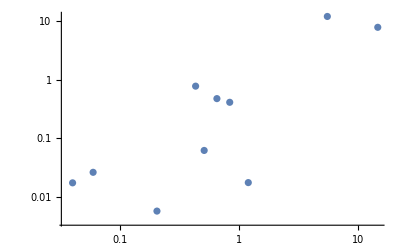

```mathematica
ListLogLogPlot[Transpose[{Transpose[ad10pars][[18]],Transpose[ad10pars][[19]]}]]
```

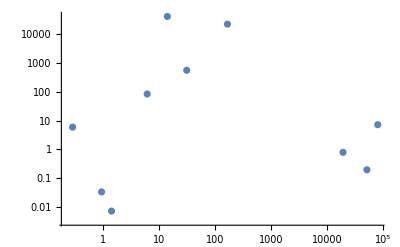

```mathematica
ListLogLogPlot[Transpose[{Transpose[us10pars][[18]],Transpose[us10pars][[19]]}]]
```

```mathematica
us1000pars=pars[[us1000index]];
```

Part::pkspec1: The expression us1000index cannot be used as a part specification.